# Numerical Solution for Functional Square Roots

## Input

Input a function and a finite range over which the solution will be found. The step size indicates the distance between the points where error is calculated.

```mathematica
f[x_]:=Sin[x]
originalRange={-2*Pi,2*Pi,0.3};
range=originalRange;
```

Here is a plot of the inputted function over the range:

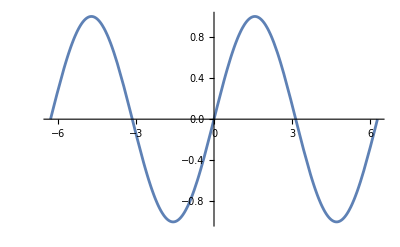

```mathematica
pRange=AbsoluteOptions[Plot[f[x], {x, range[[1]], range[[2]]}, ImageSize->Medium],PlotRange][[1,2]];
pRange[[2,1]]=Min[0,pRange[[2,1]]]; (* Set the plotting range manually *)

Plot[f[x],{x, range[[1]], range[[2]]}, PlotRange->pRange]
```

## Helper Functions

As many operations in this notebook take a very long time to run, this function gives an progress indicator for them:

```mathematica
progressMap[func_,l_List, message_:"Complete"]:=Module[{progress=PrintTemporary["0% "<>message]}, Table[NotebookDelete[progress];progress=PrintTemporary[ToString[Round[100*i/Length[l]]]<>"% "<>message]; func[l[[i]]],{i, Length[l]}]]
```

Makes a linear spline between points (i.e. connects them with straight lines), and extends the domain using the last two points on either end.

```mathematica
LinearSpline[points_][x_]:=Module[{p, m, xs,table},
p=Sort[points,#1[[1]]<#2[[1]]&];
m=If[#1==0,2^16,(#2/#1)]&@@@(Drop[p,1]-Drop[p, -1]);
table=Table[{Drop[p,-1][[i,1]]<=x<Drop[p, 1][[i,1]],m[[i]]*(x-Drop[p,1][[i,1]])+Drop[p,1][[i,2]]},{i,Length[p]-1}];
table=Flatten@Join[{x<p[[1,1]], table[[1,2]]}, table, {x>=p[[-1,1]], table[[-1,2]]}];
Which@@table
]
```

## Method 1: Exact Nested Solution from Initial X and W

## Explanation

We are trying to solve the equation g(g(x)) = f(x) for all x.
Given an initial x, xi, we can make a guess as to the value of g:
g(xi) = w
Because we know that g(g(x)) = f(x), then g(g(xi)) = f(xi), and since g(xi) = w, then:
g(w) = f(xi)
This gives a second value of g. For a third, we can repeat the same thing. g(g(x)) = f(x), so g(g(w)) = f(w), and since g(w) = f(xi):
g(f(xi)) = f(w)
If you continue this, you get as many points as you want that will all lie on the g, assuming that g(xi) = w. By searching over all xi and all w, we can find the solution which minimizes the squared difference between a linear spline of the approximating points and the original function.

This is a function which more efficiently implements the process described above:

```mathematica
approximatingPoints[xii_,w_,n_:20]:=Riffle[Transpose[{NestList[f, xii, n], NestList[f, w, n]}],Transpose[{NestList[f, w, n], NestList[f, f[xii], n]}]]
```

FInally, here are more helper functions relating to it, which are fairly self-explanatory.

```mathematica
approxFunc[xii_, w_]:=LinearSpline[approximatingPoints[xii, w]]
error[af_]:=Quiet[Sum[(af[af[x]]-f[x])^2, {x, range[[1]], range[[2]], range[[3]]}],General::munfl]
errorFunc[xii_, w_]:=error[approxFunc[xii,w]]
```

## Search

For every xii and w, the Search[] function checks the error of it, setting minP to be the values of xii and w which minimize error, and returning that minimum error. By then subdividing the region around minP, a better and better solution can be found. As the first iteration is the biggest search (in order to minimize the effect of local minima), it takes much longer than all other iterations.

```mathematica
(* Tweak the last value of each of these for faster first-step evaluation times. *)
xiiRange=range;wRange=range; 

search[anything___]:=(
points=ParallelTable[errorFunc[xii, w],{xii, xiiRange[[1]],  xiiRange[[2]],  xiiRange[[3]]}, {w, wRange[[1]],  wRange[[2]],  wRange[[3]]}];
minI=First[Position[points,Min[points],2]];
minP={xiiRange[[1]]+minI[[1]]xiiRange[[3]], wRange[[1]]+minI[[2]]wRange[[3]]};
minV=errorFunc@@minP;

xiiRange={minP[[1]]-xiiRange[[3]], minP[[1]]+xiiRange[[3]], 0.5xiiRange[[3]]};
wRange={minP[[2]]-wRange[[3]], minP[[2]]+ wRange[[3]], 0.5wRange[[3]]};

minV
);
```

```mathematica
PrintTemporary["The first step takes way longer than future steps"];
progressMap[search,Range[20]]
```

{8.31208,4.78639,3.74709,3.63145,3.54012,3.51043,3.49976,3.49548,3.49361,3.49274,3.49233,3.49212,3.49202,3.49197,3.49195,3.49193,3.49193,3.49192,3.49192,3.49192}

## Output

Based on the search, here is the best function found so far:

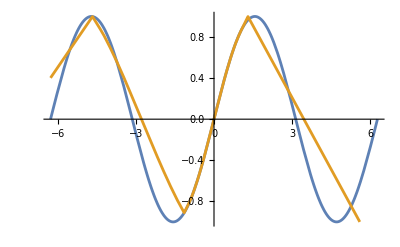

```mathematica
aFunc= approxFunc@@minP;
Plot[{f[x], aFunc[aFunc[x]]}, {x, range[[1]], range[[2]]}, PlotRange->pRange]
```

And here are the xii and w values, and the error which were achieved:

```mathematica
minP
minV
```

{-4.67068,-1.14568}

3.49192

## Method 2: Whole-Domain Numerical Minimization

## Explanation

Instead of being smart about nesting functions with a single initial guess, this method tries to determine the whole function at once in order to move the values closer to what is needed. It is extremely susceptible to local minima, but it can often do a much better job of optimizing simpler functions, such as sine or some polynomials.

First, take a guess at a functional root g. I’ve used the g from method 1 here, but you could probably use almost anything. Next, find the differences between that and the original function:
delta(x) = f(x) - g(g(x))

Finally, simply add the delta vals to g:
new_g(x) = g(x) + temperature * delta(x)

For some points, g(x) will not be affected much, but g(g(x)) will be moved closer to f. In this case, g will be positively affected. For other points, it may shoot off to infinity or become discontinuous, so there is no real guarantee that this will work.

## Implementation

First, it represents both the original function and the approximation as a set of points, with xVals being the x values of the points, fVals being the corresponding y values of the original function, and aVals being the approximated y values.

```mathematica
range[[3]]=originalRange[[3]]/5;

aFunc= approxFunc@@minP;
xVals=Range@@range;
fVals=f/@xVals;
aVals=aFunc[aFunc[#]]&/@xVals;

(* Generates the interpolating function from a list of y values *)
funcFromVals[vals_]:=LinearSpline[Transpose[{xVals,  vals}]]
```

Here are plots of the interpolated values for the original function and the function from method 1:

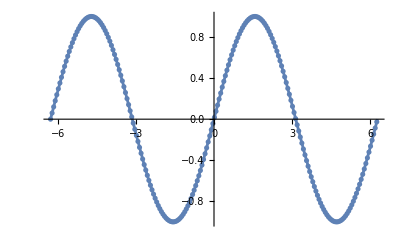

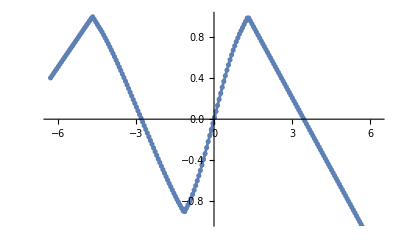

```mathematica
PlotVals[vals_]:=Show[{ListPlot[Transpose[{xVals, vals}], PlotRange->pRange], Plot[funcFromVals[vals][x], {x, range[[1]], range[[2]]}, PlotRange->pRange]}]
PlotVals[fVals]
PlotVals[aVals]
```

## Optimization

This repeatedly applies the method described to optimize the function.

```mathematica
aValsHist={aVals};
progressMap[
(aFunc=funcFromVals[aVals];
aVals=aVals+0.3*(fVals-ParallelMap[aFunc[aFunc[#]]&,xVals]);
AppendTo[aValsHist, aVals];)&,Range[50] , "Optimized"];

(* Find the optimization which actually minimized error *)
bestVals=aValsHist[[First[PositionSmallest[ParallelMap[error[funcFromVals[#]]&,aValsHist]]]]];
aFunc=funcFromVals[bestVals];
```

Plot the progress made so far:

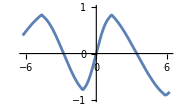
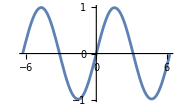
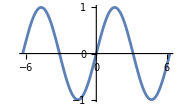
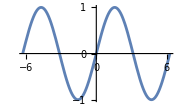
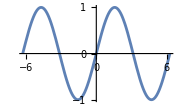

```mathematica
ParallelMap[With[{aFunc=funcFromVals[aValsHist[[#]]]},Plot[aFunc[aFunc[x]], {x, range[[1]], range[[2]]}, ImageSize->Small, PlotRange->pRange]]&, Round/@Subdivide[1, Length[aValsHist], 4]]
```

## Output

Plot the original and the best output:

-Graphics-

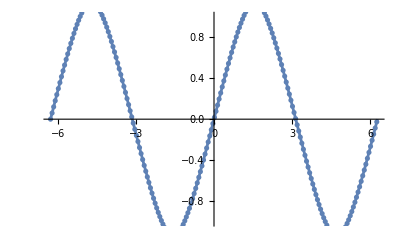

```mathematica
PlotVals[fVals]
PlotVals[bestVals]
```

## Final Approximation

```mathematica
"Method 1 Error:"
e1=error[approxFunc@@minP]
"Method 2 Error:"
e2=error[aFunc]

(* Choose the one with the least error *)
approximation=If[e1<e2,approxFunc@@minP, aFunc];
```

Method 1 Error:

20.3241

Method 2 Error:

1.60663×10^-9

A plot of the final approximation:

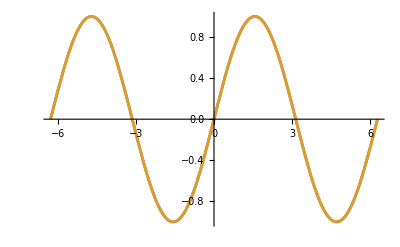

```mathematica
Plot[{f[x], approximation[approximation[x]]}, {x, range[[1]], range[[2]]}, PlotRange->pRange]
```

```mathematica
p=Transpose[{xVals, Fourier[aVals]}];
pa={#1, Abs[#2]}&@@@p;
p2=p[[15;;-15]];
pa2={#1, Abs[#2]}&@@@p2;
```

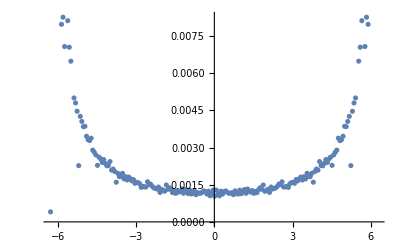

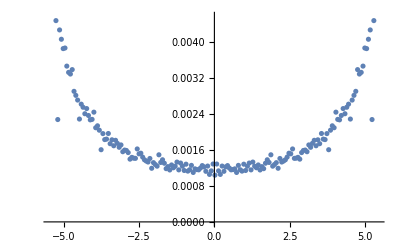

```mathematica
ListPlot[pa]
ListPlot[pa2]
```

```mathematica
fi=FindFit[pa2,a+b Cosh[c x],{a,b,c},x]
```

{a→0.0013456,b→1.9031×10^-6,c→1.57822}

```mathematica
fit=a+b Cosh[c x]/.fi
```

0.0013456+1.9031×10^-6 Cosh[1.57822 x]

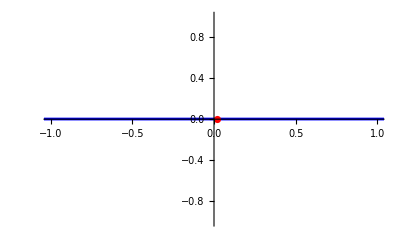

```mathematica
Show[ListPlot[p2,PlotStyle->Red],(*Plot the data points in red*)
Plot[fit,{x,Min[p2[[All,1]]],Max[p2[[All,1]]]},PlotStyle->Blue] (*Plot the fitted curve in blue*)]
```

```mathematica
ifp=InverseFourier[fit/.x->#&/@xVals];
```

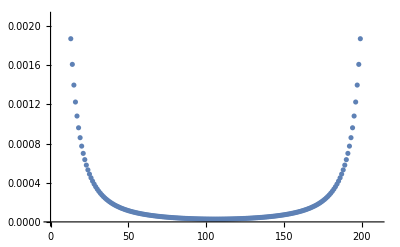

```mathematica
ListPlot[Abs/@ifp]
```

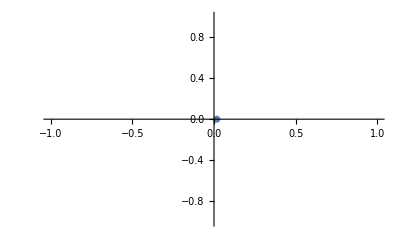

```mathematica
ifpx=Transpose[{xVals, ifp}];
ListPlot[ifpx]
```

```mathematica
fit/.{x->#}&/@Fourier[p]
```

{{0.00134881+0. ⅈ,0.00135025+0. ⅈ},{0.00134697-1.46423×10^-6 ⅈ,0.00134869+4.67137×10^-6 ⅈ},{0.00134338+8.10038×10^-7 ⅈ,0.00134058-2.60421×10^-6 ⅈ},{0.00134512+1.60051×10^-6 ⅈ,0.00134453-5.1943×10^-6 ⅈ},{0.00134501-1.5224×10^-6 ⅈ,0.00134428+5.00137×10^-6 ⅈ},{0.00134798-2.83802×10^-7 ⅈ,0.00135085+9.46982×10^-7 ⅈ},{0.00134709+1.10172×10^-6 ⅈ,0.00134885-3.74889×10^-6 ⅈ},{0.00134538+1.31868×10^-6 ⅈ,0.00134512-4.59761×10^-6 ⅈ},{0.00134418+9.56584×10^-7 ⅈ,0.00134259-3.43663×10^-6 ⅈ},{0.0013436+4.79674×10^-7 ⅈ,0.00134143-1.78799×10^-6 ⅈ},{0.00134345+7.86883×10^-8 ⅈ,0.00134121-3.06934×10^-7 ⅈ},{0.00134354-1.98769×10^-7 ⅈ,0.00134149+8.20222×10^-7 ⅈ},{0.00134376-3.60491×10^-7 ⅈ,0.00134202+1.59627×10^-6 ⅈ},{0.00134403-4.29922×10^-7 ⅈ,0.00134263+2.08302×10^-6 ⅈ},{0.00134431-4.31074×10^-7 ⅈ,0.00134323+2.35007×10^-6 ⅈ},{0.00134457-3.84528×10^-7 ⅈ,0.00134378+2.4589×10^-6 ⅈ},{0.00134482-3.05907×10^-7 ⅈ,0.00134427+2.45757×10^-6 ⅈ},{0.00134505-2.06032×10^-7 ⅈ,0.00134469+2.38108×10^-6 ⅈ},{0.00134525-9.16307×10^-8 ⅈ,0.00134505+2.25357×10^-6 ⅈ},{0.00134543+2.95763×10^-8 ⅈ,0.00134535+2.09728×10^-6 ⅈ},{0.0013456+1.54353×10^-7 ⅈ,0.0013456+1.92448×10^-6 ⅈ},{0.00134575+2.80238×10^-7 ⅈ,0.0013458+1.74426×10^-6 ⅈ},{0.0013459+4.04088×10^-7 ⅈ,0.00134597+1.56484×10^-6 ⅈ},{0.00134603+5.25848×10^-7 ⅈ,0.00134611+1.38895×10^-6 ⅈ},{0.00134616+6.45152×10^-7 ⅈ,0.00134623+1.21899×10^-6 ⅈ},{0.00134628+7.60994×10^-7 ⅈ,0.00134633+1.05732×10^-6 ⅈ},{0.00134641+8.73647×10^-7 ⅈ,0.00134641+9.04309×10^-7 ⅈ},{0.00134653+9.83561×10^-7 ⅈ,0.00134648+7.59875×10^-7 ⅈ},{0.00134665+1.09103×10^-6 ⅈ,0.00134654+6.23877×10^-7 ⅈ},{0.00134678+1.19692×10^-6 ⅈ,0.0013466+4.95534×10^-7 ⅈ},{0.00134691+1.30031×10^-6 ⅈ,0.00134665+3.7549×10^-7 ⅈ},{0.00134705+1.40259×10^-6 ⅈ,0.00134669+2.62338×10^-7 ⅈ},{0.00134719+1.50346×10^-6 ⅈ,0.00134674+1.56024×10^-7 ⅈ},{0.00134734+1.60295×10^-6 ⅈ,0.00134679+5.61642×10^-8 ⅈ},{0.00134749+1.70118×10^-6 ⅈ,0.00134683-3.77143×10^-8 ⅈ},{0.00134765+1.79803×10^-6 ⅈ,0.00134688-1.25952×10^-7 ⅈ},{0.00134782+1.89142×10^-6 ⅈ,0.00134693-2.07727×10^-7 ⅈ},{0.001348+1.98222×10^-6 ⅈ,0.00134698-2.84083×10^-7 ⅈ},{0.00134818+2.07036×10^-6 ⅈ,0.00134703-3.55437×10^-7 ⅈ},{0.00134837+2.15507×10^-6 ⅈ,0.00134709-4.2178×10^-7 ⅈ},{0.00134857+2.23579×10^-6 ⅈ,0.00134715-4.83227×10^-7 ⅈ},{0.00134877+2.31202×10^-6 ⅈ,0.00134721-5.39912×10^-7 ⅈ},{0.00134897+2.38289×10^-6 ⅈ,0.00134728-5.91766×10^-7 ⅈ},{0.00134918+2.44738×10^-6 ⅈ,0.00134734-6.38623×10^-7 ⅈ},{0.00134939+2.50426×10^-6 ⅈ,0.00134741-6.80217×10^-7 ⅈ},{0.00134959+2.55189×10^-6 ⅈ,0.00134747-7.16087×10^-7 ⅈ},{0.00134978+2.58882×10^-6 ⅈ,0.00134754-7.45849×10^-7 ⅈ},{0.00134996+2.61344×10^-6 ⅈ,0.0013476-7.69019×10^-7 ⅈ},{0.00135013+2.62419×10^-6 ⅈ,0.00134766-7.85142×10^-7 ⅈ},{0.00135028+2.6199×10^-6 ⅈ,0.00134771-7.93897×10^-7 ⅈ},{0.00135041+2.59957×10^-6 ⅈ,0.00134775-7.95012×10^-7 ⅈ},{0.0013505+2.56281×10^-6 ⅈ,0.00134779-7.8845×10^-7 ⅈ},{0.00135057+2.50969×10^-6 ⅈ,0.00134782-7.74335×10^-7 ⅈ},{0.00135061+2.44102×10^-6 ⅈ,0.00134783-7.5308×10^-7 ⅈ},{0.00135062+2.35811×10^-6 ⅈ,0.00134784-7.25269×10^-7 ⅈ},{0.00135059+2.26266×10^-6 ⅈ,0.00134784-6.91638×10^-7 ⅈ},{0.00135053+2.15695×10^-6 ⅈ,0.00134782-6.53143×10^-7 ⅈ},{0.00135045+2.04332×10^-6 ⅈ,0.0013478-6.10745×10^-7 ⅈ},{0.00135035+1.92429×10^-6 ⅈ,0.00134778-5.6549×10^-7 ⅈ},{0.00135022+1.80223×10^-6 ⅈ,0.00134775-5.18343×10^-7 ⅈ},{0.00135009+1.67927×10^-6 ⅈ,0.00134771-4.7019×10^-7 ⅈ},{0.00134994+1.55736×10^-6 ⅈ,0.00134767-4.21828×10^-7 ⅈ},{0.00134978+1.43797×10^-6 ⅈ,0.00134764-3.73878×10^-7 ⅈ},{0.00134962+1.32236×10^-6 ⅈ,0.0013476-3.26867×10^-7 ⅈ},{0.00134945+1.21137×10^-6 ⅈ,0.00134756-2.81159×10^-7 ⅈ},{0.00134929+1.10553×10^-6 ⅈ,0.00134753-2.36988×10^-7 ⅈ},{0.00134913+1.00516×10^-6 ⅈ,0.0013475-1.94487×10^-7 ⅈ},{0.00134898+9.10404×10^-7 ⅈ,0.00134748-1.53731×10^-7 ⅈ},{0.00134882+8.21547×10^-7 ⅈ,0.00134746-1.14887×10^-7 ⅈ},{0.00134868+7.38568×10^-7 ⅈ,0.00134745-7.79834×10^-8 ⅈ},{0.00134854+6.6094×10^-7 ⅈ,0.00134744-4.27528×10^-8 ⅈ},{0.00134841+5.88423×10^-7 ⅈ,0.00134744-9.0892×10^-9 ⅈ},{0.00134829+5.21541×10^-7 ⅈ,0.00134744+2.25887×10^-8 ⅈ},{0.00134817+4.59508×10^-7 ⅈ,0.00134746+5.26983×10^-8 ⅈ},{0.00134807+4.02769×10^-7 ⅈ,0.00134748+8.07851×10^-8 ⅈ},{0.00134797+3.50574×10^-7 ⅈ,0.00134751+1.07232×10^-7 ⅈ},{0.00134788+3.02855×10^-7 ⅈ,0.00134755+1.31912×10^-7 ⅈ},{0.00134781+2.59014×10^-7 ⅈ,0.00134759+1.5513×10^-7 ⅈ},{0.00134774+2.1902×10^-7 ⅈ,0.00134765+1.76715×10^-7 ⅈ},{0.00134768+1.82495×10^-7 ⅈ,0.00134771+1.96796×10^-7 ⅈ},{0.00134763+1.49151×10^-7 ⅈ,0.00134778+2.15438×10^-7 ⅈ},{0.00134758+1.18733×10^-7 ⅈ,0.00134786+2.32687×10^-7 ⅈ},{0.00134755+9.0923×10^-8 ⅈ,0.00134795+2.48685×10^-7 ⅈ},{0.00134752+6.5678×10^-8 ⅈ,0.00134805+2.63263×10^-7 ⅈ},{0.0013475+4.29616×10^-8 ⅈ,0.00134816+2.76217×10^-7 ⅈ},{0.00134749+2.23137×10^-8 ⅈ,0.00134828+2.8792×10^-7 ⅈ},{0.00134749+4.00507×10^-9 ⅈ,0.00134842+2.97755×10^-7 ⅈ},{0.00134749-1.23296×10^-8 ⅈ,0.00134856+3.05999×10^-7 ⅈ},{0.0013475-2.65353×10^-8 ⅈ,0.00134871+3.12166×10^-7 ⅈ},{0.00134752-3.86522×10^-8 ⅈ,0.00134886+3.16045×10^-7 ⅈ},{0.00134755-4.88394×10^-8 ⅈ,0.00134903+3.17643×10^-7 ⅈ},{0.00134758-5.7221×10^-8 ⅈ,0.0013492+3.16944×10^-7 ⅈ},{0.00134761-6.37084×10^-8 ⅈ,0.00134938+3.13563×10^-7 ⅈ},{0.00134765-6.83797×10^-8 ⅈ,0.00134957+3.07429×10^-7 ⅈ},{0.0013477-7.12566×10^-8 ⅈ,0.00134976+2.98385×10^-7 ⅈ},{0.00134774-7.23642×10^-8 ⅈ,0.00134995+2.86296×10^-7 ⅈ},{0.00134779-7.17087×10^-8 ⅈ,0.00135014+2.71008×10^-7 ⅈ},{0.00134784-6.93189×10^-8 ⅈ,0.00135032+2.5243×10^-7 ⅈ},{0.00134789-6.52314×10^-8 ⅈ,0.0013505+2.30505×10^-7 ⅈ},{0.00134794-5.95153×10^-8 ⅈ,0.00135067+2.05267×10^-7 ⅈ},{0.00134799-5.22738×10^-8 ⅈ,0.00135082+1.76844×10^-7 ⅈ},{0.00134803-4.36534×10^-8 ⅈ,0.00135096+1.45481×10^-7 ⅈ},{0.00134806-3.38519×10^-8 ⅈ,0.00135107+1.11558×10^-7 ⅈ},{0.00134808-2.31139×10^-8 ⅈ,0.00135115+7.55808×10^-8 ⅈ},{0.0013481-1.17238×10^-8 ⅈ,0.00135119+3.81612×10^-8 ⅈ},{0.00134811-5.27344×10^-22 ⅈ,0.00135121+2.52575×10^-21 ⅈ},{0.0013481+1.17238×10^-8 ⅈ,0.00135119-3.81612×10^-8 ⅈ},{0.00134808+2.31139×10^-8 ⅈ,0.00135115-7.55808×10^-8 ⅈ},{0.00134806+3.38519×10^-8 ⅈ,0.00135107-1.11558×10^-7 ⅈ},{0.00134803+4.36534×10^-8 ⅈ,0.00135096-1.45481×10^-7 ⅈ},{0.00134799+5.22738×10^-8 ⅈ,0.00135082-1.76844×10^-7 ⅈ},{0.00134794+5.95153×10^-8 ⅈ,0.00135067-2.05267×10^-7 ⅈ},{0.00134789+6.52314×10^-8 ⅈ,0.0013505-2.30505×10^-7 ⅈ},{0.00134784+6.93189×10^-8 ⅈ,0.00135032-2.5243×10^-7 ⅈ},{0.00134779+7.17087×10^-8 ⅈ,0.00135014-2.71008×10^-7 ⅈ},{0.00134774+7.23642×10^-8 ⅈ,0.00134995-2.86296×10^-7 ⅈ},{0.0013477+7.12566×10^-8 ⅈ,0.00134976-2.98385×10^-7 ⅈ},{0.00134765+6.83797×10^-8 ⅈ,0.00134957-3.07429×10^-7 ⅈ},{0.00134761+6.37084×10^-8 ⅈ,0.00134938-3.13563×10^-7 ⅈ},{0.00134758+5.7221×10^-8 ⅈ,0.0013492-3.16944×10^-7 ⅈ},{0.00134755+4.88394×10^-8 ⅈ,0.00134903-3.17643×10^-7 ⅈ},{0.00134752+3.86522×10^-8 ⅈ,0.00134886-3.16045×10^-7 ⅈ},{0.0013475+2.65353×10^-8 ⅈ,0.00134871-3.12166×10^-7 ⅈ},{0.00134749+1.23296×10^-8 ⅈ,0.00134856-3.05999×10^-7 ⅈ},{0.00134749-4.00507×10^-9 ⅈ,0.00134842-2.97755×10^-7 ⅈ},{0.00134749-2.23137×10^-8 ⅈ,0.00134828-2.8792×10^-7 ⅈ},{0.0013475-4.29616×10^-8 ⅈ,0.00134816-2.76217×10^-7 ⅈ},{0.00134752-6.5678×10^-8 ⅈ,0.00134805-2.63263×10^-7 ⅈ},{0.00134755-9.0923×10^-8 ⅈ,0.00134795-2.48685×10^-7 ⅈ},{0.00134758-1.18733×10^-7 ⅈ,0.00134786-2.32687×10^-7 ⅈ},{0.00134763-1.49151×10^-7 ⅈ,0.00134778-2.15438×10^-7 ⅈ},{0.00134768-1.82495×10^-7 ⅈ,0.00134771-1.96796×10^-7 ⅈ},{0.00134774-2.1902×10^-7 ⅈ,0.00134765-1.76715×10^-7 ⅈ},{0.00134781-2.59014×10^-7 ⅈ,0.00134759-1.5513×10^-7 ⅈ},{0.00134788-3.02855×10^-7 ⅈ,0.00134755-1.31912×10^-7 ⅈ},{0.00134797-3.50574×10^-7 ⅈ,0.00134751-1.07232×10^-7 ⅈ},{0.00134807-4.02769×10^-7 ⅈ,0.00134748-8.07851×10^-8 ⅈ},{0.00134817-4.59508×10^-7 ⅈ,0.00134746-5.26983×10^-8 ⅈ},{0.00134829-5.21541×10^-7 ⅈ,0.00134744-2.25887×10^-8 ⅈ},{0.00134841-5.88423×10^-7 ⅈ,0.00134744+9.0892×10^-9 ⅈ},{0.00134854-6.6094×10^-7 ⅈ,0.00134744+4.27528×10^-8 ⅈ},{0.00134868-7.38568×10^-7 ⅈ,0.00134745+7.79834×10^-8 ⅈ},{0.00134882-8.21547×10^-7 ⅈ,0.00134746+1.14887×10^-7 ⅈ},{0.00134898-9.10404×10^-7 ⅈ,0.00134748+1.53731×10^-7 ⅈ},{0.00134913-1.00516×10^-6 ⅈ,0.0013475+1.94487×10^-7 ⅈ},{0.00134929-1.10553×10^-6 ⅈ,0.00134753+2.36988×10^-7 ⅈ},{0.00134945-1.21137×10^-6 ⅈ,0.00134756+2.81159×10^-7 ⅈ},{0.00134962-1.32236×10^-6 ⅈ,0.0013476+3.26867×10^-7 ⅈ},{0.00134978-1.43797×10^-6 ⅈ,0.00134764+3.73878×10^-7 ⅈ},{0.00134994-1.55736×10^-6 ⅈ,0.00134767+4.21828×10^-7 ⅈ},{0.00135009-1.67927×10^-6 ⅈ,0.00134771+4.7019×10^-7 ⅈ},{0.00135022-1.80223×10^-6 ⅈ,0.00134775+5.18343×10^-7 ⅈ},{0.00135035-1.92429×10^-6 ⅈ,0.00134778+5.6549×10^-7 ⅈ},{0.00135045-2.04332×10^-6 ⅈ,0.0013478+6.10745×10^-7 ⅈ},{0.00135053-2.15695×10^-6 ⅈ,0.00134782+6.53143×10^-7 ⅈ},{0.00135059-2.26266×10^-6 ⅈ,0.00134784+6.91638×10^-7 ⅈ},{0.00135062-2.35811×10^-6 ⅈ,0.00134784+7.25269×10^-7 ⅈ},{0.00135061-2.44102×10^-6 ⅈ,0.00134783+7.5308×10^-7 ⅈ},{0.00135057-2.50969×10^-6 ⅈ,0.00134782+7.74335×10^-7 ⅈ},{0.0013505-2.56281×10^-6 ⅈ,0.00134779+7.8845×10^-7 ⅈ},{0.00135041-2.59957×10^-6 ⅈ,0.00134775+7.95012×10^-7 ⅈ},{0.00135028-2.6199×10^-6 ⅈ,0.00134771+7.93897×10^-7 ⅈ},{0.00135013-2.62419×10^-6 ⅈ,0.00134766+7.85142×10^-7 ⅈ},{0.00134996-2.61344×10^-6 ⅈ,0.0013476+7.69019×10^-7 ⅈ},{0.00134978-2.58882×10^-6 ⅈ,0.00134754+7.45849×10^-7 ⅈ},{0.00134959-2.55189×10^-6 ⅈ,0.00134747+7.16087×10^-7 ⅈ},{0.00134939-2.50426×10^-6 ⅈ,0.00134741+6.80217×10^-7 ⅈ},{0.00134918-2.44738×10^-6 ⅈ,0.00134734+6.38623×10^-7 ⅈ},{0.00134897-2.38289×10^-6 ⅈ,0.00134728+5.91766×10^-7 ⅈ},{0.00134877-2.31202×10^-6 ⅈ,0.00134721+5.39912×10^-7 ⅈ},{0.00134857-2.23579×10^-6 ⅈ,0.00134715+4.83227×10^-7 ⅈ},{0.00134837-2.15507×10^-6 ⅈ,0.00134709+4.2178×10^-7 ⅈ},{0.00134818-2.07036×10^-6 ⅈ,0.00134703+3.55437×10^-7 ⅈ},{0.001348-1.98222×10^-6 ⅈ,0.00134698+2.84083×10^-7 ⅈ},{0.00134782-1.89142×10^-6 ⅈ,0.00134693+2.07727×10^-7 ⅈ},{0.00134765-1.79803×10^-6 ⅈ,0.00134688+1.25952×10^-7 ⅈ},{0.00134749-1.70118×10^-6 ⅈ,0.00134683+3.77143×10^-8 ⅈ},{0.00134734-1.60295×10^-6 ⅈ,0.00134679-5.61642×10^-8 ⅈ},{0.00134719-1.50346×10^-6 ⅈ,0.00134674-1.56024×10^-7 ⅈ},{0.00134705-1.40259×10^-6 ⅈ,0.00134669-2.62338×10^-7 ⅈ},{0.00134691-1.30031×10^-6 ⅈ,0.00134665-3.7549×10^-7 ⅈ},{0.00134678-1.19692×10^-6 ⅈ,0.0013466-4.95534×10^-7 ⅈ},{0.00134665-1.09103×10^-6 ⅈ,0.00134654-6.23877×10^-7 ⅈ},{0.00134653-9.83561×10^-7 ⅈ,0.00134648-7.59875×10^-7 ⅈ},{0.00134641-8.73647×10^-7 ⅈ,0.00134641-9.04309×10^-7 ⅈ},{0.00134628-7.60994×10^-7 ⅈ,0.00134633-1.05732×10^-6 ⅈ},{0.00134616-6.45152×10^-7 ⅈ,0.00134623-1.21899×10^-6 ⅈ},{0.00134603-5.25848×10^-7 ⅈ,0.00134611-1.38895×10^-6 ⅈ},{0.0013459-4.04088×10^-7 ⅈ,0.00134597-1.56484×10^-6 ⅈ},{0.00134575-2.80238×10^-7 ⅈ,0.0013458-1.74426×10^-6 ⅈ},{0.0013456-1.54353×10^-7 ⅈ,0.0013456-1.92448×10^-6 ⅈ},{0.00134543-2.95763×10^-8 ⅈ,0.00134535-2.09728×10^-6 ⅈ},{0.00134525+9.16307×10^-8 ⅈ,0.00134505-2.25357×10^-6 ⅈ},{0.00134505+2.06032×10^-7 ⅈ,0.00134469-2.38108×10^-6 ⅈ},{0.00134482+3.05907×10^-7 ⅈ,0.00134427-2.45757×10^-6 ⅈ},{0.00134457+3.84528×10^-7 ⅈ,0.00134378-2.4589×10^-6 ⅈ},{0.00134431+4.31074×10^-7 ⅈ,0.00134323-2.35007×10^-6 ⅈ},{0.00134403+4.29922×10^-7 ⅈ,0.00134263-2.08302×10^-6 ⅈ},{0.00134376+3.60491×10^-7 ⅈ,0.00134202-1.59627×10^-6 ⅈ},{0.00134354+1.98769×10^-7 ⅈ,0.00134149-8.20222×10^-7 ⅈ},{0.00134345-7.86883×10^-8 ⅈ,0.00134121+3.06934×10^-7 ⅈ},{0.0013436-4.79674×10^-7 ⅈ,0.00134143+1.78799×10^-6 ⅈ},{0.00134418-9.56584×10^-7 ⅈ,0.00134259+3.43663×10^-6 ⅈ},{0.00134538-1.31868×10^-6 ⅈ,0.00134512+4.59761×10^-6 ⅈ},{0.00134709-1.10172×10^-6 ⅈ,0.00134885+3.74889×10^-6 ⅈ},{0.00134798+2.83802×10^-7 ⅈ,0.00135085-9.46982×10^-7 ⅈ},{0.00134501+1.5224×10^-6 ⅈ,0.00134428-5.00137×10^-6 ⅈ},{0.00134512-1.60051×10^-6 ⅈ,0.00134453+5.1943×10^-6 ⅈ},{0.00134338-8.10038×10^-7 ⅈ,0.00134058+2.60421×10^-6 ⅈ},{0.00134697+1.46423×10^-6 ⅈ,0.00134869-4.67137×10^-6 ⅈ}}

```mathematica
ListPointPlot3D[{#1, Re[#2], Im[#2]}&@@@p2, AxesLabel->{"x", "y", "z"}, PlotRange->All]
```

-Graphics3D-

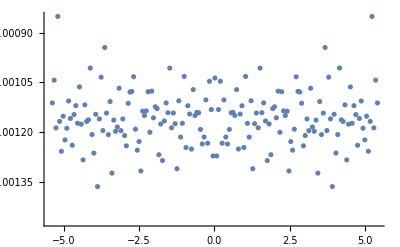

```mathematica
ListPlot[{#1, Re[#2]}&@@@p2, Axes->{True, False}]
```

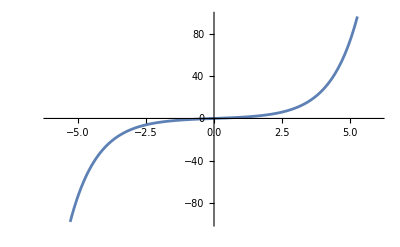

```mathematica
Plot[Sinh[x], {x, -6,6}]
```

```mathematica
Solve[{b I==s I,a==Abs[s I +r]}, {s, r}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{s→b,r→-a-ⅈ b},{s→b,r→a-ⅈ b}}

```mathematica
g=E^(I Pi z)
```

ⅇ^(ⅈ π z)

```mathematica
ComplexPlot[g, {z, 0, I+1}]
```

-Graphics-

```mathematica
gI=Im[g]
gR=Re[g]
```

Im[ⅇ^(ⅈ π z)]

Re[ⅇ^(ⅈ π z)]

```mathematica
ComplexPlot[gR + I gI, {z, 0.5, I+1}]
```

-Graphics-

```mathematica
gM=Abs[g]
```

ⅇ^(-π Im[z])

```mathematica
Plot3D[Abs[gI]/.{z->zRe+I zIm}, {zRe, 0, 1}, {zIm, 0, 1}]
```

-Graphics3D-

```mathematica
Plot3D[gM/.{z->zRe+I zIm}, {zRe, 0, 1}, {zIm, 0, 1}]
```

-Graphics3D-

```mathematica
gE=I gI -Sqrt[gM^2 -gI^2]
```

ⅈ Im[ⅇ^(ⅈ π z)]-√(ⅇ^(-2 π Im[z])-Im[ⅇ^(ⅈ π z)]^2)

```mathematica
ComplexPlot[gE, {z, 0.5, I+1}]
```

-Graphics-

```mathematica
m=Abs[z], i=Im[z]
```

```mathematica
z=a+i I
```

```mathematica
r=Sqrt[m^2 -i^2]
```

```mathematica
r=Sqrt[a]
```